# Predator Prey Model - Interaction Strength

## This script tests the interaction strength between modeled predator and prey.

### Predator-prey equations; run sample timeseries

{{x[t]→InterpolatingFunction[…][t],y[t]→InterpolatingFunction[…][t]}}

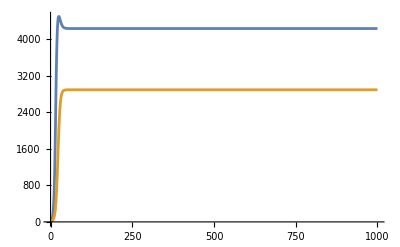

```mathematica
lv = 
   With[{rh = 0.4, kh = 5000, c = 0.1, d = 500, rp = 0.2, kp = 2000,qh = 1.0, Eh = 0.0, qp = 1.0, Ep = 0.0, 
   b = 0.1},
      With[{x0 = 10., y0 = 10.}, 
         NDSolve[
            {x'[t] == (rh * x[t]*((kh - x[t])/kh)) - (( c *x[t]*y[t])/(d + x[t])) - (qh * Eh * x[t]), 
          y'[t] == (rp * y[t]*((kp - y[t])/kp)) + (( b* x[t]* y[t])/(d + x[t])) - (qp * Ep * y[t]), 
          x[0] == x0, y[0] == y0}, 
            {x[t], y[t]}, {t, 0, 1000}]]]

Plot[Evaluate[{x[t], y[t]} /. lv], {t, 0, 1000}]
```

### Solve equations for nullclines

```mathematica
(rh * x * ((kh - x)/kh)) - ((c * x * y)/(d + x)) - (qh * Eh * x) = 0
nullclineX = Solve[(rh * x * ((kh - x)/kh)) - ((c * x * y)/(d + x)) - (qh * Eh * x) == 0, y]

(rp * y * ((kp - y)/kp)) + ((b * x * y)/(d + x)) - (qp * Ep * x) = 0
nullclineY = Solve[(rp * y * ((kp - y)/kp)) + ((b * x * y)/(d + x)) - (qp * Ep * x) == 0, x]
```

Set::write: Tag Plus in 0.+0.00008 (5000-x) x-(0.6 x y)/(500+x) is Protected.

0

{{y→-(1.66667 (500.+x) (0.-0.00008 (5000.-1. x) x))/x}}

Set::write: Tag Plus in 0.+(0.6 x y)/(500+x)+0.0001 (2000-y) y is Protected.

0

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{x→-(500. (-2000.+y))/(-8000.+y)}}

## Time Series & Phase Plane Analysis Across Interaction Strength

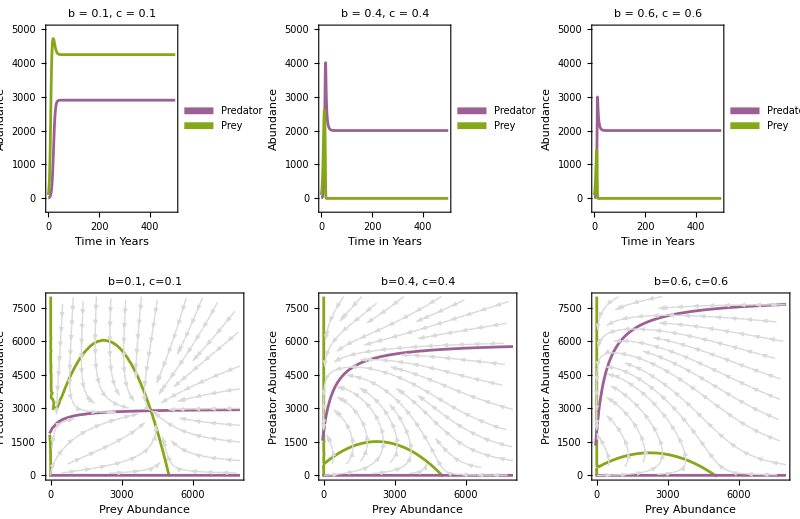

```mathematica
Clear[x,y,rh,kh,c,d,qh,Eh,rp,kp,b,qp,Ep]

(*Defining function to solve equations*)
solveSystem[b_,c_]:=NDSolve[{H'[t]==(rh*H[t]*((kh-H[t])/kh))-((c*H[t]*P[t])/(d+H[t]))-(qh*Eh*H[t]),P'[t]==(rp*P[t]*((kp-P[t])/kp))+((b*H[t]*P[t])/(d+H[t]))-(qp*Ep*P[t]),
H[0]==h0,P[0]==p0},{H[t],P[t]},{t,0,tmax},MaxStepSize->0.0001];

(*B & C value parameter combinations, Interaction strengths*)
parameterCombinations={{0.1,0.1},{0.4,0.4},{0.6,0.6}};

rh=0.4;
kh=5000;
d=500;
rp=0.2;
kp=2000;
qh=1.0;
Eh=0.0;
qp=1.0;
Ep=0.0;
h0=100;
p0=10;
tmax=500;

(*Generate and plot solutions for each interaction strength*)
plots1=Table[
(*Extract bValue and cValue from parameterCombination*)
{bValue,cValue}=parameterCombination;
(*Solve the system for the current interaction strength*)
solution=solveSystem[bValue,cValue][[1]];
(*Plot the results*)
With[{H0=10},
Plot[Evaluate[{P[t],H[t]}/. solution],{t,0,tmax},
Frame->True,FrameLabel->{ "Time in Years","Abundance"},
PlotStyle->{ColorData[98,3],ColorData[98,4]},
FrameStyle->Directive[FontFamily->"Arial",16],
AspectRatio->1,
PlotLabel->StringForm["b = ``, c = ``",bValue,cValue],
PlotLegends->Placed[SwatchLegend[{"Predator","Prey"},LegendMarkerSize->8,LegendFunction->(Framed[#,FrameMargins->0,Background->Directive[LightGray,Opacity[0.75]]]&)],{Right,Top}], LabelStyle->{FontSize->12},Frame->True,
PlotRange->{{0,tmax},{-300,5000}}]],{parameterCombination,parameterCombinations}];

(*Create a list of plots for different interaction strengths*)
plots2=Table[{b,c}=parameterCombination;
(*Nullcline for Prey*)
nullclineX=ContourPlot[(rh*x*((kh-x)/kh))-((c*x*y)/(d+x))-(qh*Eh*x)==0,{x,-50,8000},{y,-50,8000},ContourStyle->ColorData[98,4]];
(*Nullcline for Predator*)
nullclineY=ContourPlot[(rp*y*((kp-y)/kp))+((b*x*y)/(d+x))-(qp*Ep*y)==0,{x,-50,8000},{y,-50,8000},ContourStyle->ColorData[98,3]];
(*Vector field*)
vectorField=VectorPlot[{(rh*x*((kh-x)/kh))-((c*x*y)/(d+x))-(qh*Eh*x),(rp*y*((kp-y)/kp))+((b*x*y)/(d+x))-(qp*Ep*y)},{x,-50,8000},{y,-50,8000},
VectorColorFunction->None,
VectorStyle->Gray,
VectorPoints->None,
StreamPoints->Coarse,
StreamColorFunction->None,
StreamStyle->{GrayLevel[0.85],Arrowheads[0.035],Thick}];
(*Combine nullclines and vector field*)
Show[{nullclineX,nullclineY,vectorField},
PlotRange->{{-50,8000},{-50,8000}},
AxesLabel->{"x","y"},
PlotLabel->"b="<>ToString[b]<>", c="<>ToString[c],
PlotLegends->Placed[SwatchLegend[{"Predator","Prey"},
LegendMarkerSize->8,
LegendFunction->(Framed[#,FrameMargins->0,Background->Directive[LightGray,Opacity[0.75]]]&)],
{Right,Top}], 
FrameStyle->Directive[FontFamily->"Arial",16],
FrameLabel->{ "Prey Abundance","Predator Abundance"}, 
LabelStyle->{FontSize->12}],
{parameterCombination,parameterCombinations}];

(*Display the plots*)
GraphicsGrid[{plots1,plots2},ImageSize->800]
```

## Time Series & Phase Plane Analysis with Predator Fishing

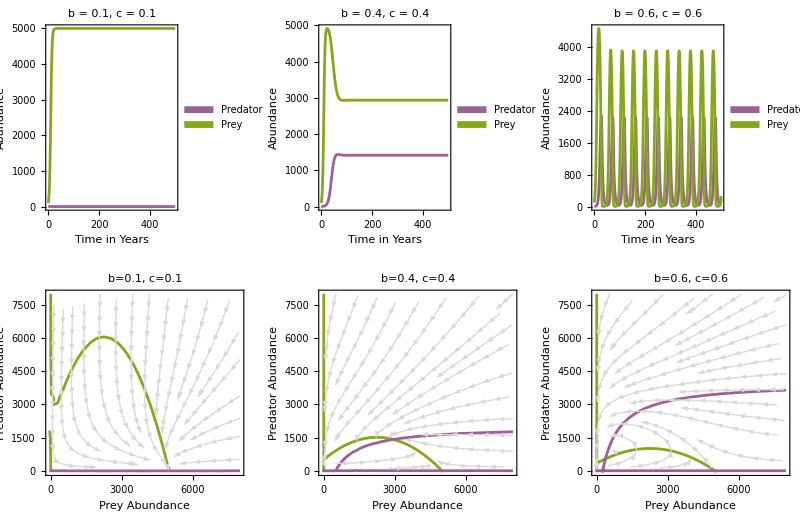

```mathematica
Clear[x,y,rh,kh,c,d,qh,Eh,rp,kp,b,qp,Ep]

(*Defining a function to solve*)
solveSystem[b_,c_]:=NDSolve[{H'[t]==(rh*H[t]*((kh-H[t])/kh))-((c*H[t]*P[t])/(d+H[t]))-(qh*Eh*H[t]),
P'[t]==(rp*P[t]*((kp-P[t])/kp))+((b*H[t]*P[t])/(d+H[t]))-(qp*Ep*P[t]),
H[0]==h0,P[0]==p0},{H[t],P[t]},{t,0,tmax},MaxStepSize->0.0001];

(*Define interaction strengths*)
parameterCombinations={{0.1,0.1},{0.4,0.4},{0.6,0.6}};

rh=0.4;
kh=5000;
d=500;
rp=0.2;
kp=2000;
qh=1.0;
Eh=0.0;
qp=1.0;
Ep=0.4;
h0=100;
p0=10;
tmax=500;

(*Generate and plot solutions for each interaction strength*)
plots1=Table[
(*Extract bValue and cValue from parameterCombination*)
{bValue,cValue}=parameterCombination;
(*Solve the system for the current interaction strength*)
solution=solveSystem[bValue,cValue][[1]];
(*Plot the results*)
With[{H0=10},
Plot[Evaluate[{P[t],H[t]}/. solution],{t,0,tmax},
Frame->True,FrameLabel->{ "Time in Years","Abundance"},
PlotStyle->{ColorData[98,3],ColorData[98,4]},
FrameStyle->Directive[FontFamily->"Arial",16],
AspectRatio->1,
PlotLabel->StringForm["b = ``, c = ``",bValue,cValue],
PlotLegends->Placed[SwatchLegend[{"Predator","Prey"},
LegendMarkerSize->8,
LegendFunction->(Framed[#,FrameMargins->0,Background->Directive[LightGray,Opacity[0.75]]]&)],{Right,Top}], 
LabelStyle->{FontSize->12},
Frame->True]],{parameterCombination,parameterCombinations}];

(*Create a list of plots for different interaction strength*)
plots2=Table[{b,c}=parameterCombination;
(*Nullcline for Prey*)
nullclineX=ContourPlot[(rh*x*((kh-x)/kh))-((c*x*y)/(d+x))-(qh*Eh*x)==0,{x,-50,8000},{y,-50,8000},ContourStyle->ColorData[98,4]];
(*Nullcline for Predator*)
nullclineY=ContourPlot[(rp*y*((kp-y)/kp))+((b*x*y)/(d+x))-(qp*Ep*y)==0,{x,-50,8000},{y,-50,8000},ContourStyle->ColorData[98,3]];
(*Vector field*)
vectorField=VectorPlot[{(rh*x*((kh-x)/kh))-((c*x*y)/(d+x))-(qh*Eh*x),(rp*y*((kp-y)/kp))+((b*x*y)/(d+x))-(qp*Ep*y)},{x,-50,8000},{y,-50,8000},
VectorColorFunction->None,
VectorStyle->Gray,
VectorPoints->None,
StreamPoints->Coarse,
StreamColorFunction->None,
StreamStyle->{GrayLevel[0.85],Arrowheads[0.035],Thick}];
(*Combine nullclines and vector field*)
Show[{nullclineX,nullclineY,vectorField},
PlotRange->{{-50,8000},{-50,8000}},
AxesLabel->{"x","y"},
PlotLabel->"b="<>ToString[b]<>", c="<>ToString[c],
PlotLegends->Placed[SwatchLegend[{"Predator","Prey"},
LegendMarkerSize->8,
LegendFunction->(Framed[#,FrameMargins->0,Background->Directive[LightGray,Opacity[0.75]]]&)],{Right,Top}], 
FrameStyle->Directive[FontFamily->"Arial",16],
FrameLabel->{ "Prey Abundance","Predator Abundance"},
 LabelStyle->{FontSize->12}],
{parameterCombination,parameterCombinations}];

(*Display the plots*)
GraphicsGrid[{plots1,plots2},ImageSize->800]
```